```mathematica
SetDirectory[NotebookDirectory[]];
```

## Explicit functions

```mathematica
names={"Constant","Linear","Quadratic","Cubic","Sine","Inverse Sine","Tangent","Inverse tangent","Positive exponential","Negative exponential","Log"};
equations = {0,x,x^2,x^3, Sin[x],ArcSin[x],Tan[x],ArcTan[x],E^x, E^(-x),Log[x]};
TraditionalForm[equations]
```

{0,x,x^2,x^3,sin(x),sin^-1(x),tan(x),tan^-1(x),ⅇ^x,ⅇ^-x,log(x)}

```mathematica
plots = Table[Plot[i,{x,0,10},PlotTheme->"Web"], {i,equations}]; (* You can remove the semicolon to see what any expression is doing *)
```

```mathematica
export = Rasterize[Grid[Transpose[{names, equations, plots}], Frame->All]]
Export["Table 1.png",export]
```

-Graphics-

Table 1.png

## Conic Sections

```mathematica
conics = {"Circle"-> x^2+y^2-4,"Ellipse" -> x^2+3y^2-9, "Parabola" -> x^2-y, "Hyperbola" -> y^2-x^2-1}
```

{Circle→-4+x^2+y^2,Ellipse→-9+x^2+3 y^2,Parabola→x^2-y,Hyperbola→-1-x^2+y^2}

```mathematica
labels[x_]:=Transpose[x/.Rule->List][[1]]
eqns[x_]:=Transpose[x/.Rule->List][[2]]
```

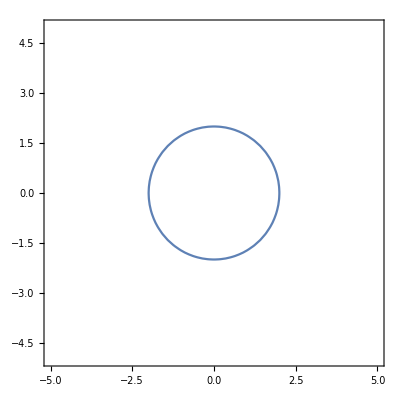
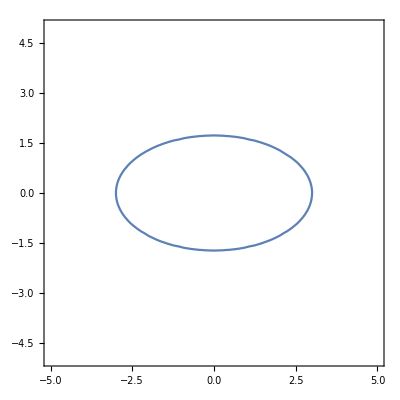
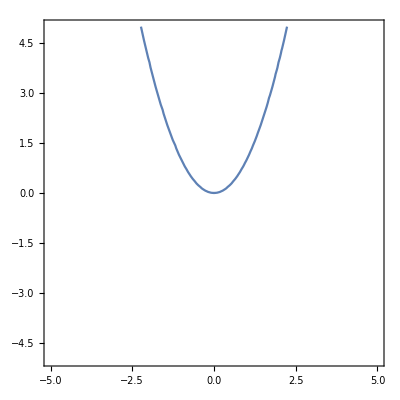
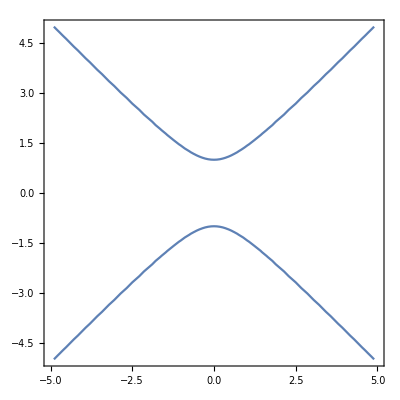

```mathematica
imPlots = Table[ContourPlot[i==0,{x,-5,5}, {y,-5,5}], {i,eqns[conics]}]
```

```mathematica
export = Rasterize[Grid[Transpose[{labels[conics], Table[TraditionalForm[i==0],{i,eqns[conics]}], imPlots}], Frame->All]]
Export["Table 2.png",export]
```

-Graphics-

Table 2.png

## Overlaid graphs

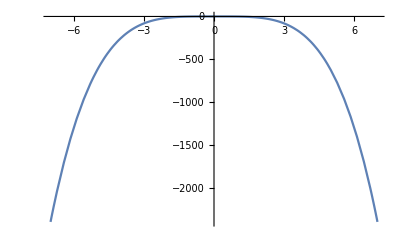
-Graphics--Graphics-

```mathematica
Overlay[Reverse[{Plot[-x^4,{x,-7,7}],ImageResize[Import["sketches/AppleTop.png"],400]}]]
```

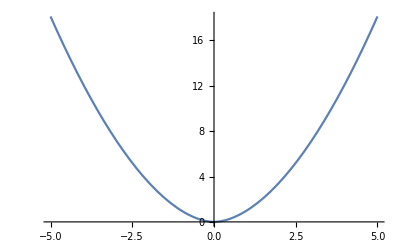

```mathematica
Plot[Abs[x]^1.8, {x,-5,5}]
```

```mathematica
Export["/home/eric/git/QEA/Module 1/Set 1: Curves and Surfaces/plot.png",%338,"PNG"]
```

/home/eric/git/QEA/Module 1/Set 1: Curves and Surfaces/plot.png

```mathematica
TraditionalForm[Abs[x]^1.8]
```

Abs[x]^1.8

## Quadratic Surfaces

```mathematica
surfaces = {"Plane" -> x, "Elipsoid" -> 2 x^2 + y^2 + 3z^2 - 16,"One-sheet Hyperboloid"-> x^2 + y^2 - z^2-4, "Hyperbolic Parabaloid" ->3 x^2 - 3y^2 +10 z};
```

```mathematica
imPlots3 := Table[ContourPlot3D[i==0,{x,-5,5}, {y,-5,5}, {z,-5,5}], {i,eqns[surfaces]}]
imPlots3
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
export = Rasterize[Grid[Transpose[{labels[surfaces], Table[TraditionalForm[i==0],{i,eqns[surfaces]}], imPlots3}], Frame->All]]
Export["Table 3.png",export];
```

-Graphics-

## Implicitly defining an apple

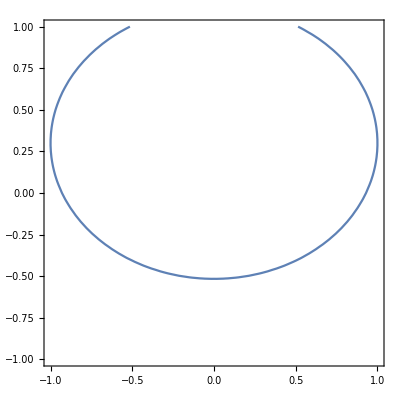

```mathematica
ContourPlot[x^2+1.5(y-0.3)^2==1,{x,-1,1},{y,-1,1}]
```

```mathematica
Manipulate[ContourPlot3D[z^2 + i(Sqrt[x^2+y^2]-i2)^2 ==1, {x,-2,2},{y,-2,2},{z,-2,2}],{i,0.6,1.4}, {i2,-1,1}]
```

```mathematica
export = Rasterize[ContourPlot3D[z^2 + 1.4(Sqrt[x^2+y^2]-.7)^2 ==1, {x,-1.6,1.6},{y,-1.6,1.6},{z,-1.6,1.6}], RasterSize -> 800]
Export["Apple.png", export];
```

-Graphics-